```mathematica
ClearAll["Global`*"];
Clear[Derivative];
l0=1;
l1=1;
m0 = 0.25;
m1 = 0.25;
s =FullSimplify[DSolve[{p00'[x] == -(2m0+l0)p00[x]+m1 p01[x],
p11'[x]==-(2m1+l1)p11[x]+m0 p01[x],
p01'[x]==2m0 p00[x]+2m1 p11[x]-(m0+m1)p01[x],
p00[0]==1,p11[0]==0,p01[0]==0},
{p00[x],p11[x],p01[x]},x]]
ss={p00[x],p11[x],p01[x]}/.First@s
```

{{p00[x]→0.426777 ⅇ^(-1.70711 x)+0.5 ⅇ^(-1.5 x)+0.0732233 ⅇ^(-0.292893 x),p01[x]→-0.353553 ⅇ^(-1.70711 x)-4.69442×10^-17 ⅇ^(-1.5 x)+0.353553 ⅇ^(-0.292893 x),p11[x]→0.426777 ⅇ^(-1.70711 x)-0.5 ⅇ^(-1.5 x)+0.0732233 ⅇ^(-0.292893 x)}}

{0.426777 ⅇ^(-1.70711 x)+0.5 ⅇ^(-1.5 x)+0.0732233 ⅇ^(-0.292893 x),0.426777 ⅇ^(-1.70711 x)-0.5 ⅇ^(-1.5 x)+0.0732233 ⅇ^(-0.292893 x),-0.353553 ⅇ^(-1.70711 x)-4.69442×10^-17 ⅇ^(-1.5 x)+0.353553 ⅇ^(-0.292893 x)}

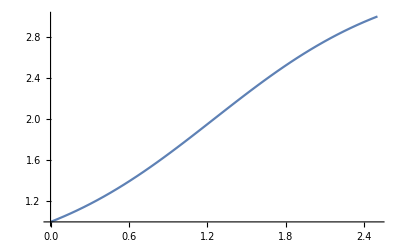

3.00354

```mathematica
Plot[1/l[x],{x,0,2.5}]
1/l[2.5]
```

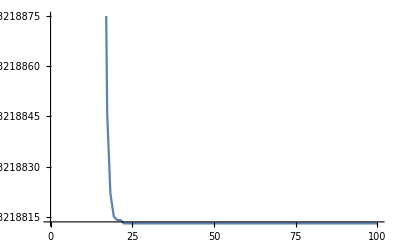

```mathematica
ff[x_] :=Log[f1[x]+f2[x]+f3[x]]
Plot[-ff'[x],{x,0,100}]
```

```mathematica
f1[x_]:=0.4267766952966368 ⅇ^(-1.7071067811865477 x)+0.5000000000000001 ⅇ^(-1.5000000000000018 x)+0.07322330470336312 ⅇ^(-0.29289321881345254 x)
f2[x_]:=0.4267766952966369 ⅇ^(-1.7071067811865477 x)-0.5000000000000001 ⅇ^(-1.5000000000000018 x)+0.07322330470336316 ⅇ^(-0.29289321881345254 x)
f3[x_]:=-0.35355339059327373 ⅇ^(-1.7071067811865477 x)-4.694417451709621*^-17 ⅇ^(-1.5000000000000018 x)+0.3535533905932738 ⅇ^(-0.29289321881345254 x)
l[x_]:=(f1[x]+f2[x])/(f1[x]+f2[x]+f3[x])
1/l[2.5]
```

3.00354

```mathematica
1/l[2*0.8498749999999999]
2.43838814565
```

2.43839

2.43839